```mathematica
Clear[src,outp];
src=NotebookDirectory[];
outp=src~~"output\\";
Get[
"https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2022_aerosol_quantification/myPackageWL.wl"];

evalfiles = Get["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2022_aerosol_quantification/url-evaluation-files.m"];
```

### evaluate respiratory data

```mathematica
transl=.
transl={"variable","date","time","name","atmospheric pressure","temperature","humidity","height above German reference surface","tidal volume","breathing frequency","expiratory reserve volume","inspiratory vital capacity","expiratory vital capacity","forced expiratory volume 1 sec","forced vital capacity","peak expiratory flow","maximal (mid-)expiratory flow 25%","maximal (mid-)expiratory flow 50%","maximal (mid-)expiratory flow 75%","residual volume","total lung capacity","alveolar volume","functional residual capacity","haemoglobin","inspiratory concentration helium","expiratory concentration helium","inspiratory concentration carbon monoxide","expiratory concentration carbon monoxide","diffusion capacitance carbon monoxide"};

exportlist=.
exportlist={{"ID","age","height","sex","dlco","tlco","kcosi","kcotr","inspiratory_concentration_helium","expiratory_concentration_helium","inspiratory_concentration_carbon_monoxide","expiratory_concentration_carbon_monoxide","va","ethnic","fev1","fvc","maximal_(mid-)expiratory_flow_25%","fef2575","fef75","fev075","peak_expiratory_flow","frc","tlc","rv","erv","ic","expiratory_vital_capacity","vc","tidal_volume","breathing_rate_1/min","atmospheric_pressure","temperature","humidity","height_above_German_reference_surface"}};

Map[
(respData=.;
respData=StringSplit[Import[#[[3]]],"\n"];
respData=StringSplit[Flatten@respData[[15;;Length@respData]],"  "]/.""->Nothing;
respData[[All,1]]=StringReplace[#,{DigitCharacter->"",".94"->"oe"}]&/@respData[[All,1]];
respData[[1]]=Prepend[respData[[1]],"Variable"];
respData=StringReplace[#," "->""]&/@respData;
respData[[All,1]]=transl;
(*TableForm[respData]*)

varProb=.;
varProb=Import[#[[2]]];
varProb=Flatten[StringCases[varProb,#]&/@{"Geschlecht--" ~~Shortest[a__]~~","->a,"Geburtsjahr--" ~~Shortest[a__]~~","->a,"Groesse--" ~~Shortest[a__]~~","->a}];
varProb=varProb/.{"maennlich"->"M","weiblich"->"F","divers"->"M"};
varProb[[2]]=2023-ToExpression[varProb[[2]]];
varProb;

AppendTo[exportlist,varProb[[{2,3,1}]]];
(*
TableForm[Transpose[Prepend[{respData},Table[i,{i,Length@respData}]]]]
*)

PrependTo[exportlist[[-1]],StringCases[respData[[4,2]],DigitCharacter..][[1]]]; (*ID*)


AppendTo[exportlist[[-1]],{"",respData[[-1,4]],"","",respData[[25,4]],respData[[26,4]],respData[[27,4]],respData[[28,4]],respData[[22,4]],0,respData[[14,4]],respData[[15,4]],respData[[17,4]],respData[[18,4]],respData[[19,4]],"",respData[[16,4]],respData[[23,4]],respData[[21,4]],respData[[20,4]],respData[[11,4]],respData[[12,4]],respData[[13,4]],"",Min[ToExpression/@respData[[9,-3;;-1]]] (*Slow Vital Capacity != tidal volume*),Min[ToExpression/@respData[[10,-3;;-1]]] ,StringCases[respData[[5,2]],DigitCharacter..][[1]],
StringCases[respData[[6,2]],DigitCharacter..][[1]],
StringCases[respData[[7,2]],DigitCharacter..][[1]],
StringCases[respData[[8,2]],DigitCharacter..][[1]]
}];
exportlist=Map[Flatten[#]&,exportlist,{1}];

)&,evalfiles];
Export[outp~~"lung function testing.xlsx",exportlist]
```

C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\output\lung function testing.xlsx

## Upload on http://gli-calculator.ersnet.org/index.html for explanation see http://gli-calculator.ersnet.org/docs.html

```mathematica
replList=.
fn=.
fn=Import["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2022_aerosol_quantification/full%20names%20GLI%20variables.xlsx"];
replList=(#[[1]]->#[[2]])&/@Partition[Flatten@fn,2];

(*
idList=.
idList=StringReplace[Flatten[StringCases[evalfiles[[All,3]],"\\"~~NumberString ..~~"\\"]],"\\"->""];
PrependTo[idList,"ID"];
*)

respData=.
respData=Import["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2022_aerosol_quantification/lung%20function%20testing_GLI.xlsx"][[1]];

(*
respData=Map[Flatten[#]&,Transpose[{idList,respData}],{1}];
*)


z=0;
delList=.
delList=Map[(z=z+1;If[Union[#[[2;;-1]]]=={0},z,Nothing])&,Transpose@respData];
 (*lösche Spalten mit 0*)

respData=Transpose@Delete[Transpose@respData,{#}&/@delList];
respData[[1]]=respData[[1]]/.replList;


cvTOvcMale=.
cvTOvcMale[age_Real]:=Module[{},{0.562+0.357 *age,"±2 SEE:",4.15}] (*Closing Volume as % of vital capacity  with 2 Standrad Deviations*)
cvTOvcFemale=.
cvTOvcFemale[age_Real]:=Module[{},{2.812+0.293 *age,"±2 SEE:",4.90}]
(* the closing volume is the endexpiratory volume before total expiration. the here calculated volume is the volume, where no bronchiole closing occurs (the non-closing-volume)  *)
closingVolume=.
closingVolume[l_List]:=Module[{f},If[l[[4]]=="M",f=cvTOvcMale,f=cvTOvcFemale];{f[l[[2]]],{(1-(f[l[[2]]][[1]]/100))*l[[22]],f[l[[2]]][[-1]]*l[[22]]/100}}]

cvList=Transpose[closingVolume/@Rest@respData];
PrependTo[cvList[[1]],"closing volume as percent of vital capacity with 2 Std Dev [from Buis & Ross: Predicted Values for Closing Volumes(...). Amer Rev of Resp Dis 1973]"];
PrependTo[cvList[[2]],"vital capacity - closing volume with 2 Std Dev [from Buis & Ross: Predicted Values for Closing Volumes(...). Amer Rev of Resp Dis 1973]"];

respData=Join[Transpose@respData,cvList];

respDataXLSX=respData;
respDataXLSX[[-2]][[2;;-1]]=StringJoin[ToString@#[[1]]~~" ± "~~ToString@#[[-1]]]&/@Rest@respDataXLSX[[-2]];
respDataXLSX[[-1]][[2;;-1]]=StringJoin[ToString@#[[1]]~~" ± "~~ToString@#[[-1]]]&/@Rest@respDataXLSX[[-1]];

Export[outp~~"lung function testing with GLI references.xlsx",Transpose@respDataXLSX]

Export[outp~~"lung function testing with GLI references.m",Transpose@respData]
```

C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\output\lung function testing with GLI references.xlsx

C:\Users\mona_\CloudStation\Forschung\GitHub\my-data-storage\data\2022_aerosol_quantification\output\lung function testing with GLI references.m

#### for output see https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2022_aerosol_quantification/lung%20function%20testing%20with%20GLI%20references.xlsx https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2022_aerosol_quantification/evaluated%20Pexa%20measurements.m

```mathematica
test=.
test=Rest[Select[respData,StringContainsQ[#[[1]],"Alveolar Volume Percent Predicted"]&][[1]]];
FindDistribution@test
CDF[FindDistribution@test]
```

MixtureDistribution[{0.576957,0.423043},{NormalDistribution[88.2198,6.16958],UniformDistribution[{76.351,121.426}]}]

Function[x,Piecewise[{{0.+0.288478 Erfc[0.114612 (88.2198-x)], x<76.351}, {0.423043+0.288478 Erfc[0.114612 (88.2198-x)], x>121.426}, {0.00938532 (-76.351+x)+0.288478 Erfc[0.114612 (88.2198-x)], True}}],Listable]

```mathematica
data=.
data=Select[respData,StringContainsQ[#[[1]],"Percent Predicted"]&]
```

{{FEV1 Percent Predicted,70.933,103.258,90.617,104.362,112.338,116.758,93.13,85.005,79.897,84.963,83.834,93.111,86.76,90.301,94.377,99.072,105.987,94.281,86.366,121.639,99.218,107.068,97.711,92.603,91.305,87.785,90.225,93.548,74.171,84.973,95.477},{FVC Percent Predicted,79.544,95.536,89.332,96.51,110.254,119.82,102.273,86.68,81.326,84.567,99.062,91.659,85.076,82.6,94.236,108.849,96.784,113.35,90.719,124.611,112.371,104.445,92.325,97.718,94.344,92.409,93.526,93.088,82.542,94.1,95.304},{FEV1/FVC Percent Predicted,89.141,108.094,101.398,106.398,100.847,97.694,90.92,98.257,97.716,100.517,84.755,101.445,101.783,108.838,100.066,90.742,108.006,82.629,94.663,98.177,88.079,103.24,105.817,94.367,96.987,94.517,96.,100.906,89.718,90.459,100.442},{TLCO Percent Predicted,93.448,97.881,88.552,74.082,82.849,101.832,130.446,78.236,81.487,100.357,87.48,98.496,104.498,85.712,104.981,96.852,87.675,84.961,65.817,98.018,88.4,72.601,70.056,106.603,93.894,72.101,88.457,90.542,86.848,69.842,92.813},{Alveolar Volume Percent Predicted,79.567,101.379,91.106,78.481,88.69,100.619,112.848,85.157,76.351,80.982,87.724,90.897,86.974,96.546,102.19,101.683,91.395,97.771,84.108,121.426,94.397,92.108,90.917,109.839,89.228,83.362,89.892,84.337,81.739,83.308,91.003},{FRC Percent Predicted,118.724,106.849,103.468,68.236,89.167,113.079,96.537,93.009,88.925,92.931,81.649,103.905,65.788,153.167,111.757,126.176,93.025,130.545,141.713,146.027,110.22,121.671,115.57,113.178,88.411,154.914,96.387,112.397,79.749,86.59,81.657},{TLC Percent Predicted,76.335,95.272,87.335,75.961,83.554,95.441,109.182,81.332,73.699,77.877,82.65,86.532,84.57,92.681,97.037,96.727,84.201,94.594,81.337,114.699,91.026,86.733,85.81,105.4,84.862,80.5,86.048,80.48,79.755,78.457,85.315},{RV Percent Predicted,118.217,101.072,101.778,68.619,72.855,110.225,151.508,93.326,100.413,105.325,82.235,88.505,94.571,218.557,150.61,110.495,88.892,118.781,78.429,148.803,93.202,102.46,96.861,111.521,89.598,204.436,102.988,92.137,106.572,74.939,88.788},{RVTLC Percent Predicted,154.19,108.441,116.048,90.66,87.572,116.54,141.131,116.132,136.807,136.358,101.171,105.117,112.624,236.273,156.308,114.746,106.061,126.375,97.766,131.372,102.886,119.471,114.665,106.557,106.991,254.902,120.138,115.986,132.483,97.075,105.63},{ERV Percent Predicted,122.808,121.539,106.601,71.404,146.035,149.773,48.53,100.117,85.67,87.529,87.27,139.9,42.02,107.489,79.428,144.81,105.153,151.202,209.477,159.061,134.365,159.915,168.281,118.026,98.107,122.628,92.249,150.675,68.046,110.692,77.931},{IC Percent Predicted,118.507,135.802,135.237,121.666,131.259,148.151,143.966,113.147,101.844,119.168,116.833,129.251,111.801,101.938,131.336,140.06,119.986,152.636,120.339,141.953,141.086,118.308,112.561,134.067,126.279,124.926,124.121,108.533,128.121,126.815,122.009}}

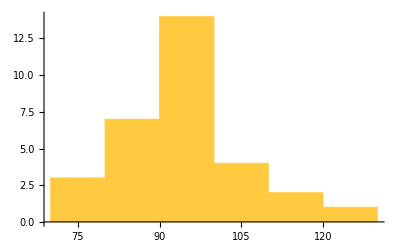
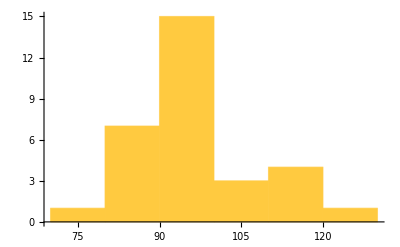
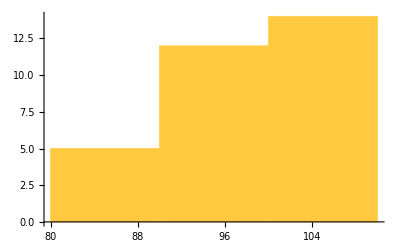
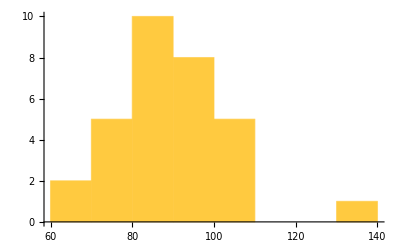
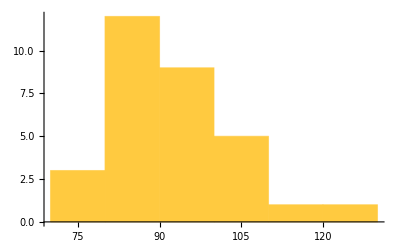
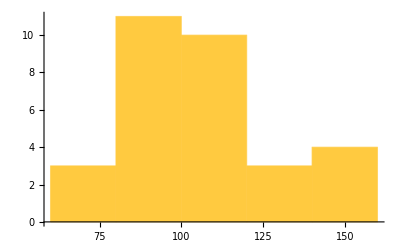
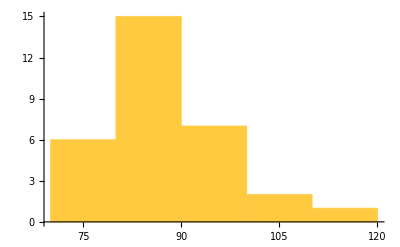
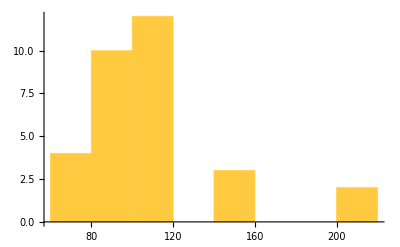
-Graphics- | FEV1 Percent Predicted
-Graphics- | FVC Percent Predicted
-Graphics- | FEV1/FVC Percent Predicted
-Graphics- | TLCO Percent Predicted
-Graphics- | Alveolar Volume Percent Predicted
-Graphics- | FRC Percent Predicted
-Graphics- | TLC Percent Predicted
-Graphics- | RV Percent Predicted
-Graphics- | RVTLC Percent Predicted
-Graphics- | ERV Percent Predicted
-Graphics- | IC Percent Predicted

```mathematica
TableForm@Transpose@{Histogram/@Rest/@data,data[[All,1]]}
```

```mathematica
respData
```